```mathematica
ψ0[x_]:=Piecewise[{{x, 0≤x≤1/2}, {1-x, 1/2<x≤1}}]
```

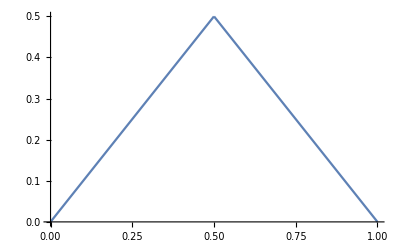

```mathematica
Plot[ψ0[x],{x,0,1}]
```

```mathematica
diffEq=D[ψ[x,t],t]==D[ψ[x,t],{x,2}]
```

ψ^(0,1)[x,t]==ψ^(2,0)[x,t]

```mathematica
bc0=ψ[0,t]==0
```

ψ[0,t]==0

```mathematica
bc1=ψ[1,t]==0
```

ψ[1,t]==0

```mathematica
bc2=ψ[x,0]==ψ0[x]
```

ψ[x,0]==(Piecewise[{{x, 0≤x≤1/2}, {1-x, 1/2<x≤1}, {0, True}}])

```mathematica
sol=DSolve[{diffEq,bc0,bc1,bc2},ψ[x,t],{x,t}]
```

{{ψ[x,t]→(4 ⅇ^(-π^2 t K[1]^2) Sin[1/2 π K[1]] Sin[π x K[1]])/(π^2 K[1]^2)K[1]1∞}}

```mathematica
f[x_,t_]:=∑_(k=1)^100 (4 ⅇ^(-π^2 t k^2)Sin[π/2 k]Sin[π x k])/(π^2 k^2)
```

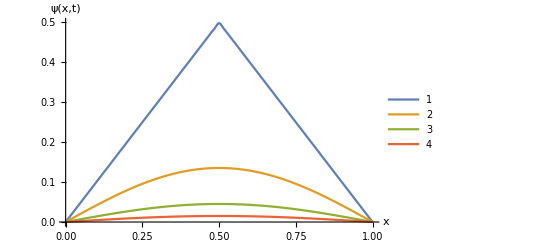

```mathematica
Plot[{f[x,0],f[x,1/9],f[x,2/9],f[x,3/9]},{x,0,1},PlotRange->{0,0.5},AxesLabel->{"x","ψ(x,t)"},PlotLegends->Automatic]
```